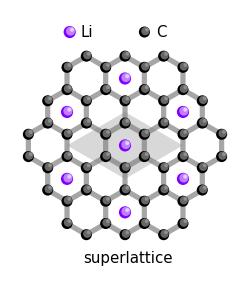
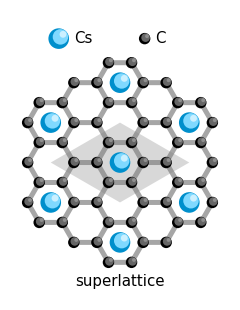

```mathematica
ColL1=Black;
NR=4;
a=(4π)/(3 √3);
a1=a/2{3,√3};
a2=a/2{3,-√3};
δ1=-a{1,0};
δ4=(√3)/2 a{0,1};
Oax={8,5};

r30:=RotationTransform[ π/6];
r60:=RotationTransform[ π/3];

SeqAxArr=Sequence[Black,Opacity[1],Thickness[0.01],Arrowheads[0.05]];
ArrowSeq=Sequence[Hue[0.55,0.8,1],Thickness[0.015],Arrowheads[0.09],Opacity[1]];
SText[str_,r_]:=Sequence[Black,Text[Style[str,15,FontFamily->"CMU Serif"],r]];
OText[str_,r_]:=Sequence[Hue[0.4,1,.8],Text[Style[str,10,FontFamily->"CMU Serif"],r]];
Rlist=Flatten[Table[{a1 i+a2 j,a1 i+a2 j+δ1},{i,-NR,NR},{j,-NR,NR}],2];
Rlist=DeleteCases[Rlist,{x_,y_}/;(x-a)^2+(y)^2>7 NR^2];
Rlist30=Map[r30,Rlist];
a1Li=√3(r60[a1]);
a2Li=√3(r60[a2]);
RlistLi=Flatten[Table[a1Li i+a2Li j+a2Li/3,{i,-NR,NR},{j,-NR,NR}],1];
RlistLi=DeleteCases[RlistLi,{x_,y_}/;(x-a)^2+(y)^2>7 NR^2];
(*RlistLi=Map[rθ,RlistLi];*)
a1Cs=2a1;
a2Cs=2a2;
RlistCs=Flatten[Table[a1Cs i+a2Cs j-δ1,{i,-NR,NR},{j,-NR,NR}],1];
RlistCs=DeleteCases[RlistCs,{x_,y_}/;(x-a)^2+(y)^2>7 NR^2];

Gatom[r_]:=Sequence[
Hue[0.6,0.0,0],Map[Disk[#,0.6]&,r],(*Atoms*)
Hue[0.6,0.0,.5 .8 ],Map[Disk[#,0.45]&,(rᵀ+{1,1}0.1)ᵀ],(*first reflection*)
Hue[0.6,0.0,.7 .8],Map[Disk[#,0.2]&,(rᵀ+{1,1}0.25)ᵀ] (*second reflection*)
];
Liatom[r_]:=Sequence[
Hue[0.75,1,1],Map[Disk[#,0.6 1.1]&,r],(*Atoms*)
Hue[0.75,0.5,1],Map[Disk[#,0.45 1.1]&,(rᵀ+{1,1}0.1)ᵀ],(*first reflection*)
Hue[0.75,0.2,1],Map[Disk[#,0.2 1.1]&,(rᵀ+{1,1}0.25)ᵀ] (*second reflection*)
];

Csatom[r_]:=Sequence[
Hue[0.55,1,.8],Map[Disk[#,0.6 1.8]&,r],(*Atoms*)
Hue[0.55,0.5,1],Map[Disk[#,0.45 1.8]&,(rᵀ+{1,1}0.1 1.8)ᵀ],(*first reflection*)
Hue[0.55,0.2,1],Map[Disk[#,0.2 1.8]&,(rᵀ+{1,1}0.25 1.8)ᵀ] (*second reflection*)
];
LiSLG=Show[
Quiet[NearestNeighborGraph[Rlist30,EdgeStyle->Directive[Gray,Thickness[0.015]]]],
Graphics[{
Gray,Opacity[0.3],Polygon[({{0,0},√3 a1,√3(a1+a2),√3 a2,{0,0}}ᵀ+√3 δ1+δ4/√3)ᵀ],
Opacity[1],
Gatom[{{+4.2,13.5}}],
SText["C",{6.,13.5}],
Liatom[{{-3.9,13.5}}],
SText["Li",{-2,13.5}],
Gatom[Rlist30],
Liatom[RlistLi],
SText[" superlattice",{a,-11}],
OText["",{-0,2.4}],
OText["",{-0.,-.1}],
OText["",{2.1,3.6}],
OText["",{2.1,-1.3}],
OText["",{4.2,2.4}],
OText["",{4.2,-.1}],
OText["",{2,1.1}+{.1,.1}8]
}],ImageSize->250];
CsSLG=Show[
Quiet[NearestNeighborGraph[Rlist,EdgeStyle->Directive[Gray,Thickness[0.015]]]],
Graphics[{
Gray,Opacity[0.3],Polygon[({{0,0},a1Cs,a1Cs+a2Cs,a2Cs,{0,0}}ᵀ+2δ1)ᵀ],
Opacity[1],
Gatom[{{+5,13}}],
SText["C",{6.7,13}],
Csatom[{{-4,13}}],
SText["Cs",{-1.4,13}],
Gatom[Rlist],
Csatom[RlistCs],
SText[" superlattice",{a,-12.5}],
OText["",{-2.3,-.1}],
OText["",{-0.,-.1}],
OText["",{1.3,2.}],
OText["",{1.3,-2.2}],
OText["",{3.7,2}],
OText["",{3.7,-2.2}],
OText["",{4.9,-.1}],
OText["",{7.4,-.1}],
OText["",{2.5,-.1}+{.12,.07}10]
}],ImageSize->240];
Row[{LiSLG,CsSLG}]
```

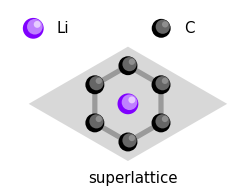
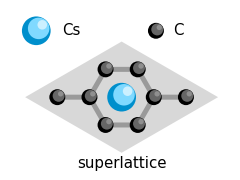

```mathematica
Rlist=Flatten[Table[{a1 i+a2 j,a1 i+a2 j+δ1},{i,-NR,NR},{j,-NR,NR}],2];
(*Rlist=DeleteCases[Rlist,{x_,y_}/;(x-a)^2+(y)^2>7 NR^2];*)
Rlist=DeleteCases[Rlist,{x_,y_}/;(x-a)^2+1.7(y)^2>2 NR^2];
RlistCs=Flatten[Table[a1Cs i+a2Cs j-δ1,{i,-NR,NR},{j,-NR,NR}],1];
RlistCs=DeleteCases[RlistCs,{x_,y_}/;(x-a)^2+(y)^2>2 NR^2];

LiSLG=Show[
Quiet[NearestNeighborGraph[Rlist30,EdgeStyle->Directive[Gray,Thickness[0.015]]]],
Graphics[{
Gray,Opacity[0.3],Polygon[({{0,0},√3 a1,√3(a1+a2),√3 a2,{0,0}}ᵀ+√3 δ1+δ4/√3)ᵀ],
Opacity[1],
Gatom[{{+4.2,13.5}}],
SText["C",{6.,13.5}],
Liatom[{{-3.9,13.5}}],
SText["Li",{-2,13.5}],
Gatom[Rlist30],
Liatom[RlistLi],
SText[" superlattice",{a,-11}]
}],ImageSize->250];
CsSLG=Show[
Quiet[NearestNeighborGraph[Rlist,EdgeStyle->Directive[Gray,Thickness[0.015]]]],
Graphics[{
Gray,Opacity[0.3],Polygon[({{0,0},a1Cs,a1Cs+a2Cs,a2Cs,{0,0}}ᵀ+2δ1)ᵀ],
Opacity[1],
Gatom[{{+5,13-8}}],
SText["C",{6.7,13-8}],
Csatom[{{-4,13-8}}],
SText["Cs",{-1.4,13-8}],
Gatom[Rlist],
Csatom[RlistCs],
SText[" superlattice",{a,-12.5}+{0,7.5}],
OText["",{-2.3,-.1}],
OText["",{-0.,-.1}],
OText["",{1.3,2.}],
OText["",{1.3,-2.2}],
OText["",{3.7,2}],
OText["",{3.7,-2.2}],
OText["",{4.9,-.1}],
OText["",{7.4,-.1}],
OText["",{2.5,-.1}]

}],ImageSize->240];
Rlist=Flatten[Table[{a1 i+a2 j,a1 i+a2 j+δ1},{i,-NR,NR},{j,-NR,NR}],2];
Rlist=DeleteCases[Rlist,{x_,y_}/;(x-a)^2+(y)^2>7 NR^2];
Rlist30=Map[r30,Rlist];
Rlist30=DeleteCases[Rlist30,{x_,y_}/;(x-a)^2+(y-0.4a)^2>0.9 NR^2];
a1Li=√3(r60[a1]);
a2Li=√3(r60[a2]);
RlistLi=Flatten[Table[a1Li i+a2Li j+a2Li/3,{i,-NR,NR},{j,-NR,NR}],1];
RlistLi=DeleteCases[RlistLi,{x_,y_}/;(x-a)^2+(y-a)^2>0.5 NR^2];
LiSLG=Show[
Quiet[NearestNeighborGraph[Rlist30,EdgeStyle->Directive[Gray,Thickness[0.015]]]],
Graphics[{
Gray,Opacity[0.3],Polygon[({{0,0},√3 a1,√3(a1+a2),√3 a2,{0,0}}ᵀ+√3 δ1+δ4/√3)ᵀ],
Opacity[1],
Gatom[{{+4.2,13.5-7.5}}],
SText["C",{6.,13.5-7.5}],
Liatom[{{-3.9,13.5-7.5}}],
SText["Li",{-2,13.5-7.5}],
Gatom[Rlist30],
Liatom[RlistLi],
SText[" superlattice",{a,-11+7.5}],
OText["",{-0,2.4}],
OText["",{-0.,-.1}],
OText["",{2.1,3.6}],
OText["",{2.1,-1.3}],
OText["",{4.2,2.4}],
OText["",{4.2,-.1}],
OText["",{2.1,1.2}]
}],ImageSize->250];
Row[{LiSLG,CsSLG}]
```

```mathematica
a=(4π)/(3 √3);
d=1.5a;
CArrow[r_]:=Sequence[Orange,Opacity[1],Thickness[0.03],Arrowheads[0.15],Arrow[BSplineCurve[({{0.2a,0},{0.5a,0.3a},{.9a,0}}ᵀ+r)ᵀ]]];
hopLi=Show[
Graphics[{
Gatom[{{0,0}}],
Gatom[{{a,0}}],
CArrow[{0,.9}],
SText["",{0.5a,.8a}],
Gatom[{{0,-d}}],
Liatom[{{a,-d}}],
CArrow[{0,.9-d}],
SText["",{0.5a,-.6a}],
Liatom[{{0,-2d}}],
Liatom[{{a,-2d}}],
CArrow[{0,.9-2d}],
SText["",{0.5a,-2.1a}]
}],ImageSize->65];
hopCs=Show[
Graphics[{
Gatom[{{0,0}}],
Gatom[{{a,0}}],
CArrow[{0,.9}],
SText["",{0.5a,.85a}],
Gatom[{{0,-d}}],
Csatom[{{a,-d}}],
CArrow[{0,1.2-d}],
SText["",{0.5a,-.5a}],
Csatom[{{0,-2.1d}}],
Csatom[{{1a,-2.1d}}],
CArrow[{0,.9-2.d}],
SText["",{0.5a,-2.15a}]
}],ImageSize->75];
Row[{hopLi,hopCs}]
```

-Graphics--Graphics-

```mathematica
CsFig=GraphicsRow[{CsSLG,hopCs},Spacings->10];
LiFig=GraphicsRow[{LiSLG,hopLi},Spacings->10];
Fig=GraphicsColumn[{CsFig,LiFig},Spacings->-10]
(*Export[FileNameJoin[{NotebookDirectory[],"Fig_lattices.pdf"}],Fig]*)
(*Export[FileNameJoin[{NotebookDirectory[],"Fig_Cs_lattice.pdf"}],CsFig]
Export[FileNameJoin[{NotebookDirectory[],"Fig_Li_lattice.pdf"}],LiFig]*)
```

-Graphics-

```mathematica
σLi=Import[FileNameJoin[{NotebookDirectory[],"Sigma_LiG.pdf"}]]
```

{-Graphics-}

```mathematica
Fig=GraphicsRow[{LiFig,σLi[[1]]},Spacings->-10]
```

-Graphics-

```mathematica
σLi[[1]]
```

```mathematica
p=0.95;
Katom[r_]:=Sequence[
Hue[0.,1,.8 p],Map[Disk[#,0.6 1.8]&,r],(*Atoms*)
Hue[0.,0.5,1 p],Map[Disk[#,0.45 1.8]&,(rᵀ+{1,1}0.1 1.8)ᵀ],(*first reflection*)
Hue[0.,0.2,1 p],Map[Disk[#,0.2 1.8]&,(rᵀ+{1,1}0.25 1.8)ᵀ] (*second reflection*)
];
Tbatom[r_]:=Sequence[
Hue[0.15,1,.8 p],Map[Disk[#,0.6 1.8]&,r],(*Atoms*)
Hue[0.15,0.5,1p],Map[Disk[#,0.45 1.8]&,(rᵀ+{1,1}0.1 1.8)ᵀ],(*first reflection*)
Hue[0.15,0.2,1p],Map[Disk[#,0.2 1.8]&,(rᵀ+{1,1}0.25 1.8)ᵀ] (*second reflection*)
];
```

```mathematica
Rlist1D=Table[{a i,0},{i,-NR,NR}];
Rlist1Dint=Table[{a i+  RandomReal[0.2a{-1,1}],-a 0.8+  RandomReal[0.2a{-1,1}]},{i,-NR,NR}];
Rlist1Dads=Table[{a i+  RandomReal[0.2a{-1,1}],+1.3a+  RandomReal[0.2a{-1,1}]},{i,-NR,NR}];
```

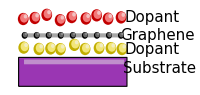

```mathematica
Diag1=Show[
NearestNeighborGraph[Rlist1D,EdgeStyle->Directive[Gray,Thickness[0.015]]],
Graphics[{
(*Gatom[(Rlist1Dᵀ+{0,3a})ᵀ],*)
Gatom[Rlist1D],
Tbatom[Rlist1Dint],
Katom[Rlist1Dads],
EdgeForm[Black],Hue[0.8,0.7,0.7],Rectangle[{-(NR +0.5)a,-3.7 a},{(NR +0.5)a ,-1.6a},RoundingRadius->0.6],
EdgeForm[None],Hue[0.8,0.3,0.8],Rectangle[{-(NR+0.5) a 0.9,-2.1a },{(NR+0.5) a 0.95,-1.75a},RoundingRadius->0.6],
SText["Dopant",{16,1.3 a}],
SText["Graphene",{17,0}],
SText["Dopant",{16,-a}],
SText["Substrate",{17.5,-2.4a}]
}],
ImageSize->200]
```

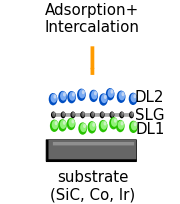

/Users/saulherrera/Documents/Projects/Optical Signatures in Doped G Superlattices/Fig_Diag.pdf

```mathematica
Katom[r_]:=Sequence[
Hue[0.6,1,.8 p],Map[Disk[#,0.6 1.8]&,r],(*Atoms*)
Hue[0.6,0.5,1 p],Map[Disk[#,0.45 1.8]&,(rᵀ+{1,1}0.1 1.8)ᵀ],(*first reflection*)
Hue[0.6,0.2,1 p],Map[Disk[#,0.2 1.8]&,(rᵀ+{1,1}0.25 1.8)ᵀ] (*second reflection*)
];
Tbatom[r_]:=Sequence[
Hue[0.3,1,.8 p],Map[Disk[#,0.6 1.8]&,r],(*Atoms*)
Hue[0.3,0.5,1p],Map[Disk[#,0.45 1.8]&,(rᵀ+{1,1}0.1 1.8)ᵀ],(*first reflection*)
Hue[0.3,0.2,1p],Map[Disk[#,0.2 1.8]&,(rᵀ+{1,1}0.25 1.8)ᵀ] (*second reflection*)
];
dt=-1.8;
dys=-0.5;
SWText[str_,r_]:=Sequence[White,Text[Style[str,15,FontFamily->"CMU Serif"],r]];
DArrow[r_]:=Sequence[Orange,Opacity[1],Thickness[0.015],Arrowheads[0.1],Arrow[{{0,12},{0,7}}]];
Diag2=Show[
NearestNeighborGraph[Rlist1D,EdgeStyle->Directive[Gray,Thickness[0.015]]],
Graphics[{
(*Gatom[(Rlist1Dᵀ+{0,3a})ᵀ],*)
Gatom[Rlist1D],
Tbatom[Rlist1Dint],
Katom[Rlist1Dads],
EdgeForm[Black],Hue[0.6,0.0,0.0.8],Rectangle[{-(NR +0.5)a 1.05,(-3.a+dys)1.05},{(NR +0.5)a ,-1.6a+dys},RoundingRadius->0.4],
EdgeForm[None],Hue[0.6,0.0,.5 0.8],Rectangle[{-(NR +0.5)a,-3. a+dys},{(NR +0.5)a ,-1.6a+dys},RoundingRadius->0.4],
EdgeForm[None],Hue[0.6,0.0,0.7 0.8],Rectangle[{-(NR+0.5) a 0.9,-2.a +dys},{(NR+0.5) a 0.95,-1.75a+dys},RoundingRadius->0.6],
SText["Adsorption+
Intercalation",{0,17}],
SText["DL2",{16+dt,1.3 a}],
SText["SLG",{16.1+dt,0}],
SText["DL1",{16+dt,-a}],
(*SWText["substrate",{0,-2.4a-.7+dys}],*)
SText["substrate
(SiC, Co, Ir)",{0,-2.4a-.7+dys-5.3}],
DArrow[{0,0}]
}],
ImageSize->180]
Export[FileNameJoin[{NotebookDirectory[],"Fig_Diag.pdf"}],Diag2]
```

```mathematica
Fig=GraphicsRow[{Diag2,LiFig,CsFig},Spacings->-10]
Export[FileNameJoin[{NotebookDirectory[],"Fig_Lattices_new.pdf"}],Fig]
```

-Graphics-

/Users/saulherrera/Documents/Projects/Optical Signatures in Doped G Superlattices/Fig_Lattices_new.pdf

```mathematica
DFTLi=Import[FileNameJoin[{NotebookDirectory[],"DFT_Li.txt"}],"Table"];
DFTLi=Drop[DFTLi,2];
DFTLi//Dimensions;
n=DeleteDuplicates[DFTLi[[All,1]]];
EnkLiDFT=Table[
l=Select[DFTLi,#[[1]]==i&];
{l[[All,2]]ᵀ,l[[All,3]]}ᵀ,
{i,n}];

TBLi=Import[FileNameJoin[{NotebookDirectory[],"TB_Li.txt"}],"Table"];
TBLi=Drop[TBLi,1];
TBLi//Dimensions;
n=DeleteDuplicates[TBLi[[All,1]]]
EnkLiTB=Table[
l=Select[TBLi,#[[1]]==i&];
{l[[All,2]]ᵀ,l[[All,3]]}ᵀ,
{i,n}];
k=EnkLiDFT[[1]][[All,1]];
klabelsLi={k[[1]],k[[91]],k[[181]],k[[271]]};

DFTCs=Import[FileNameJoin[{NotebookDirectory[],"DFT_Cs.txt"}],"Table"];
DFTCs=Drop[DFTCs,1];
DFTCs//Dimensions;
n=DeleteDuplicates[DFTCs[[All,1]]];
EnkCsDFT=Table[
l=Select[DFTCs,#[[1]]==i&];
{l[[All,2]]ᵀ,l[[All,3]]}ᵀ,
{i,n}];

TBCs=Import[FileNameJoin[{NotebookDirectory[],"TB_Cs.txt"}],"Table"];
TBCs=Drop[TBCs,1];
TBCs//Dimensions;
n=DeleteDuplicates[TBCs[[All,1]]]
EnkCsTB=Table[
l=Select[TBCs,#[[1]]==i&];
{l[[All,2]]ᵀ,l[[All,3]]}ᵀ,
{i,n}];
k=EnkCsDFT[[1]][[All,1]];
klabelsCs={k[[1]],k[[91]],k[[181]],k[[271]]};
```

{1,2,3,4,5,6,7}

{1,2,3,4,5,6,7,8,9}

```mathematica
]]
```

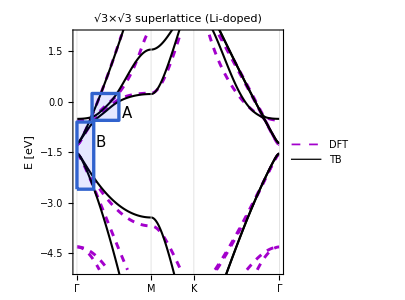
-Graphics--Graphics-

```mathematica
qpathTicksLi={{klabelsLi[[1]],"Γ"},{klabelsLi[[2]],"M"},{klabelsLi[[3]],"K"},{klabelsLi[[4]],"Γ"}};
qpathTicksCs={{klabelsCs[[1]],"Γ"},{klabelsCs[[2]],"M"},{klabelsCs[[3]],"K"},{klabelsCs[[4]],"Γ"}};
DFTseq=Sequence[Hue[0.8,1,.8],Dashed,Thickness[0.007]];
TBseq=Sequence[Black,Thickness[0.005]];
TextSeq=Sequence[Black,15,FontFamily->"CMU Serif"];
pltSeq=Sequence[GridLinesStyle->{{Directive[Dashed]},{}}, ImageSize->180,FrameTicksStyle->Directive[TextSeq],
LabelStyle->Directive[TextSeq],PlotRangePadding->0,  FrameStyle->Directive[Black,Thick],FrameLabel->{{"E [eV]"(*None*),None},{None,None}},Axes->False];
SText[str_,r_]:=Sequence[Black,Text[Style[str,TextSeq],r]];
lgnd=Placed[LineLegend[{Directive[DFTseq],Directive[TBseq]},{Style["DFT",TextSeq],Style["TB",TextSeq]},LegendFunction->(Framed[#,Background->White,FrameStyle->Thickness[1.3]]&),Spacings->0.3],{0.78,0.15}];
RectSeq=Sequence[EdgeForm[{Gray,Opacity[0.1]}],Hue[0.85,1,1],Opacity[.3]];
insetbackseq=Sequence[Hue[0.65,1,1],Opacity[.1]];
RectSeq=Sequence[EdgeForm[{Blue,Thickness[0.008]}],insetbackseq];
BandsLi=Show[
ListPlot[EnkLiDFT[[All]],Joined->True,PlotRange->{-5,2},ImageSize->300,AspectRatio->1,PlotStyle->{{DFTseq}},GridLines->{klabelsLi,None},FrameTicks->{{Automatic,{None}},{qpathTicksLi,None}},PlotLabel->Style["√3×√3 superlattice (Li-doped)",TextSeq],pltSeq,PlotLegends->lgnd],
ListPlot[EnkLiTB[[All]],Joined->True,PlotStyle->{{TBseq}},pltSeq],Graphics[{RectSeq,Rectangle[{0,-2.6},{0.1,-.6}]}],
Graphics[{RectSeq,Rectangle[{0.09,-.55},{.25,.25}]}],
Graphics[{SText["B",{.14,-1.2}]}],
Graphics[{SText["A",{.3,-.35}]}]];
InsetSeq=Sequence[Frame->True,ImageSize->150,AspectRatio->1,GridLines->{klabelsLi,None},Axes->False,PlotStyle->{{Black,Thickness[0.01]}},FrameTicks->{None,Automatic},FrameTicksStyle->Directive[TextSeq],
LabelStyle->Directive[TextSeq],PlotRangePadding->0,  FrameStyle->Directive[Blue,Thick]];
OpArrow[r_]:=Graphics[{Sequence[Hue[0.93,1,1],Opacity[1],Thickness[0.02],Arrowheads[0.1],Arrow[r]]}];
OpArrow2[r_]:=Graphics[{Sequence[Hue[0.11,1,1],Opacity[1],Thickness[0.02],Arrowheads[0.1],Arrow[r]]}];
insetsLi=GraphicsColumn[{
Show[ListPlot[EnkLiTB[[All]],Joined->True,PlotRange->{{0.09,0.25},{-.55,0.25}},AspectRatio->0.9,InsetSeq,Prolog->{Directive[insetbackseq],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],
OpArrow[{{0.18,-.26},{0.18,-.09}}],
OpArrow[({{0.18,-.26},{0.18,-.09}}ᵀ+{0.02,0.1})ᵀ],
OpArrow[({{0.18,-.24},{0.18,-.09}}ᵀ+{-0.02,-0.1})ᵀ],
Graphics[{Background->Directive[(*Hue[0.85,1,1],Opacity[0.3]*)White],SText[" A ",{.107,0.15}]}]
],
Show[ListPlot[EnkLiTB[[All]],Joined->True,PlotRange->{{0,0.1},{-2.6,-.6}},AspectRatio->1.5,InsetSeq,(*Background->Directive[Hue[0.3,1,1],Opacity[0.1]],*)
Prolog->{Directive[insetbackseq],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],
OpArrow[{{0.05,-1.88},{0.05,-0.9}}],
OpArrow[({{0.05,-2.06},{0.05,-0.74}}ᵀ+{0.01,0.})ᵀ],
OpArrow[({{0.05,-1.8},{0.05,-0.92}}ᵀ+{-0.01,0})ᵀ],
Graphics[{Background->Directive[(*Hue[0.85,1,1],Opacity[0.3]*)White],SText[" B ",{.01,-0.75}]}]
]
},Spacings->-30,ImagePadding->{{0,0},{0,20}}];
LibandsPanel=Row[{BandsLi,insetsLi}]
```

```mathematica
σ=ToExpression@Import["/Users/saulherrera/Documents/Cálculos/Optical Signatures in Doped G Superlattices/LiG/Data_Li/400_1_0.01_0._4_1500/filling_-1.764_1.236_0.1/σ.csv"];
```

Import::nffil: File /Users/saulherrera/Documents/Cálculos/Optical Signatures in Doped G Superlattices/LiG/Data_Li/400_1_0.01_0._4_1500/filling_-1.764_1.236_0.1/σ.csv not found during Import.

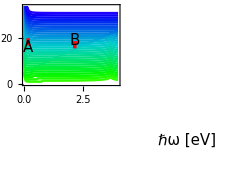

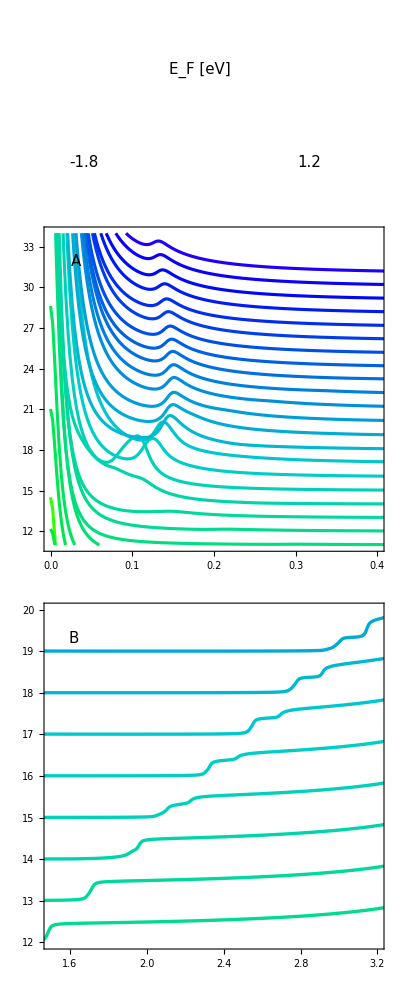

```mathematica
σ=ToExpression@Import["/Users/saulherrera/Documents/Projects/Optical Signatures in Doped G Superlattices/LiG/Data_Li/400_1_0.01_0._4_1500/filling_-1.764_1.236_0.1/σ.csv"];
ColsMag[x_]:=Blend[{{0.,Hue[0.99]},{1,Hue[0.65]}},x];
ColsPy[x_]:=Blend[{{0,Hue[0.3]},{0.5,Hue[0.5,1,0.8]},{1,Hue[0.7]}},x];
ColsG[x_]:=Blend[{{0.,Hue[0.2,1,1]},{0.5,Hue[0.1]},{1,Hue[0.0]}},x];
Cols=ColsPy;
μVHSs={0.236};μVHS=μVHSs[[1]];Temp=1;μ0=μVHS-2.0;μf=μVHS+1.0;δμ=0.1;
μlistkbT=Table[{i,1 Temp },{i,μ0,μf,δμ}];
nμc=(μlistkbT//Length);
μColors= Table[{Cols[i/nμc],Thickness[0.007]},{i,0,nμc}];
μColorsi= Table[{Cols[i/nμc],Thickness[0.015]},{i,0,nμc}];
PlotSeq=Sequence[Joined->True,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[TextSeq],
LabelStyle->Directive[TextSeq](*,ImageSize->250*)];
ColLeg=BarLegend[{Cols,{0,1}},(*LegendLabel->"E_F",*) LabelStyle->Directive[TextSeq],LegendLayout->"Row","Ticks"->{0,1},"TickLabels"->None,ImageSize->100];
ArrowSeq=Sequence[Hue[0.99],Arrowheads[0.05],Thickness[0.01]];
RecSeq=Sequence[EdgeForm[Gray],Opacity[0]];
δσ=1;ωf=4; ω0=0.0;
PltR={{ω0 ,ωf},{0,34}};
PltRi1={{ω0 ,0.1ωf},{11,34}};
PltRi2={{1.5 ,0.8ωf},{12,20}};
σCurves=Table[{σ[[i,All,1]]ᵀ,σ[[i,All,2]]+i δσ}ᵀ,{i,σ//Length}];
plotLiσ=Graphics[{
Inset[ListPlot[σCurves,PlotStyle->μColors,AspectRatio->1.4,ImageSize->250,PlotSeq,
PlotRange->PltR,
FrameLabel->{(*"ℏω [eV]"*)None,"σ(ω) [4ℏ/e^2]"},(*PlotLabel->Style[(*"Li-doped SLG"*)"√3×√3 superlattice",Black],*)
Epilog->{
ArrowSeq,Arrow[{{2.15,18},{2.15,15.6}}],Arrow[{{0.16,17.5},{0.16,20}}],
Text[Style["A",TextSeq,Background->White],{0.16,16}],
Text[Style["B",TextSeq,Background->White],{2.15,19}]
}],{0,0.05}],
Inset[Graphics[{SText["ℏω [eV]",{0,0}]}],{0.15,-1.22}]
},PlotRange->{{-1,1},{-1,1}1.3},ImageSize->250]

inset1=ListPlot[σCurves,PlotStyle->μColorsi,ImageSize->150,AspectRatio->1,PlotSeq,PlotRange->PltRi1,Epilog->{Text[Style["A",TextSeq,Background->White],{0.031,31.9}]}];
inset2=ListPlot[σCurves,PlotStyle->μColorsi,ImageSize->160,AspectRatio->1,PlotSeq,PlotRange->PltRi2,Epilog->{Text[Style["B",TextSeq,Background->White],{1.62,19.3}]}];
LegLi=Graphics[{Inset[ColLeg,{0.5,.2}],
SText["E_F [eV]",{0.55,.35}],
SText["-1.8",{0.23,.08}],
SText["1.2",{0.85,.08}]
},PlotRange->{{0.1,1},{0,.5}},ImageSize->150];

insetsLiσ=GraphicsColumn[{
LegLi,
inset1,
inset2
},Spacings->0,ImagePadding->{{0,0},{0,0}}]
```

```mathematica
LisigmaPanel=Graphics[{
Inset[plotLiσ,{0.93,0}],
Inset[insetsLiσ,{2.47,0.1}]
},PlotRange->{{0,3},{-1 0.88,1.}1.4},ImageSize->400]
```

-Graphics-

```mathematica
PlotLi=Show[
Graphics[{
SText["(a)",{0.1,0.9}],
SText["(b)",{2.7,0.9}],
Inset[LibandsPanel,{1.35,0}],
Inset[LisigmaPanel,{3.82,-.0}]
},PlotRange->{{0.05,5.},{-0.96,0.9}1.05}],ImageSize->850
]
Export[FileNameJoin[{NotebookDirectory[],"Fig_Li.pdf"}],PlotLi]
```

-Graphics-

/Users/saulherrera/Documents/Projects/Optical Signatures in Doped G Superlattices/Fig_Li.pdf

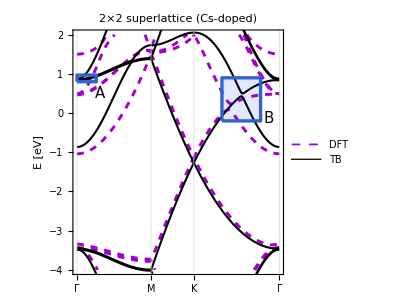
-Graphics--Graphics-

```mathematica
BandsCs=Show[
ListPlot[EnkCsDFT[[All]],Joined->True,PlotRange->{-4,2},ImageSize->300,AspectRatio->1,PlotStyle->{{DFTseq}},GridLines->{klabelsCs,None},FrameTicks->{{Automatic,{None}},{qpathTicksCs,None}},PlotLabel->Style["2×2 superlattice (Cs-doped)",TextSeq],pltSeq,PlotLegends->lgnd],
ListPlot[EnkCsTB[[All]],Joined->True,PlotStyle->{{TBseq}},pltSeq],
Graphics[{RectSeq,Rectangle[{0.75,-.2},{0.95,.9}]}],
Graphics[{RectSeq,Rectangle[{0,0.8},{.1,0.97}]}],
Graphics[{SText["A",{.12,0.5}]}],
Graphics[{SText["B",{0.99,-.15}]}]];
(*{0,0.7},{.4,1.5}*)
insetsCs=GraphicsColumn[{
Show[ListPlot[EnkCsTB[[All]],Joined->True,Frame->True,PlotRange->{{0.,0.1},{0.8,0.97}},AspectRatio->0.9,InsetSeq,Prolog->{Directive[insetbackseq],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],
OpArrow[{{0.05,0.86},{0.05,0.89}}],
OpArrow[({{0.05,0.86},{0.05,0.89}}ᵀ+{0.015,0.017})ᵀ],
OpArrow[({{0.05,0.86},{0.05,0.89}}ᵀ+{-0.013,-0.01})ᵀ],
Graphics[{Background->Directive[White],SText[" A ",{.011,0.95}]}]
],
Show[ListPlot[EnkCsTB[[All]],Joined->True,Frame->True,PlotRange->{{0.75,0.95},{-.2,0.9}},AspectRatio->1.5,InsetSeq,(*Background->Directive[Hue[0.3,1,1],Opacity[0.1]],*)
Prolog->{Directive[insetbackseq],Rectangle[Scaled[{0,0}],Scaled[{1,1}]]}],
OpArrow2[{{0.852,-.2},{0.852,0.465+.01}}],
OpArrow2[({{0.853,-.2},{0.853,0.46}}ᵀ+{-.04,-.165})ᵀ],
OpArrow2[({{0.853,-.2},{0.853,0.46}}ᵀ+{-.08,-.38})ᵀ],
OpArrow[({{0.833,.38},{0.833,0.7}}ᵀ+{0,0})ᵀ],
OpArrow[({{0.833,.38},{0.833,0.66}}ᵀ+{0.04,-.11})ᵀ],
Graphics[{Background->Directive[White],SText[" B ",{.772,0.82}]}],
Graphics[{Inset[Style["×",35,Hue[0.4,1,.85]],{0.853,0.15},{Center,Center}]}]
]
},Spacings->-30,ImagePadding->{{0,0},{0,30}}];
CsbandsPanel=Row[{BandsCs,insetsCs}]
```

```mathematica
σ=ToExpression@Import["/Users/saulherrera/Documents/Cálculos/Optical Signatures in Doped G Superlattices/CsG/Data_Cs/400_1_0.01_0._5_1500/filling_-1.16048_1.83952_0.1/σ.csv"];
```

-1.16048

1.83952

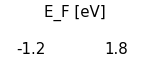

-Graphics-

```mathematica
σ=ToExpression@Import["/Users/saulherrera/Documents/Projects/Optical Signatures in Doped G Superlattices/CsG/Data_Cs/400_1_0.01_0._5_1500/filling_-1.16048_1.83952_0.1/σ.csv"];
ColsMag[x_]:=Blend[{{0.,Hue[0.99]},{1,Hue[0.65]}},x];
ColsPy[x_]:=Blend[{{0,Hue[0.3]},{0.5,Hue[0.5,1,0.8]},{1,Hue[0.7]}},x];
ColsG[x_]:=Blend[{{0.,Hue[0.2,1,1]},{0.5,Hue[0.1]},{1,Hue[0.0]}},x];
Cols=ColsPy;
μVHSs={0.431523,0.839523,0.889523,1.413857,1.733857};μVHS=μVHSs[[2]];
Temp=1;
μ0=μVHS-2.0
μf=μVHS+1.0
δμ=0.1;
μlistkbT=Table[{i,Temp },{i,μ0,μf,δμ}];

nμc=(μlistkbT//Length);
μColors= Table[{Cols[i/nμc],Thickness[0.007]},{i,0,nμc}];
μColorsi= Table[{Cols[i/nμc],Thickness[0.015]},{i,0,nμc}];
PlotSeq=Sequence[Joined->True,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[TextSeq],
LabelStyle->Directive[TextSeq](*,ImageSize->250*)];
ColLeg=BarLegend[{Cols,{0,1}},(*LegendLabel->"E_F",*) LabelStyle->Directive[TextSeq],LegendLayout->"Row","Ticks"->{0,1},"TickLabels"->None,ImageSize->100];
ArrowSeq=Sequence[Hue[0.99],Arrowheads[0.05],Thickness[0.01]];
RecSeq=Sequence[EdgeForm[Gray],Opacity[0]];

δσ=1;ωf=5; ω0=0.;
PltR={{ω0,ωf},{0,33}};
PltRi1={{0,.2},{5,37}};
PltRi2={{3,4},{13,19}};
σCurves=Table[{σ[[i,All,1]]ᵀ,σ[[i,All,2]]+i δσ}ᵀ,{i,σ//Length}];
plotCsσ=Graphics[{
Inset[ListPlot[σCurves,PlotStyle->μColors,PlotSeq,AspectRatio->1.4,ImageSize->250,PlotSeq,
PlotRange->PltR,
FrameLabel->{(*"ℏω [eV]"*)None,"σ(ω) [4ℏ/e^2]"},
Epilog->{
ArrowSeq,Arrow[{{3.52,18},{3.52,15.7}}],Arrow[{{0.4,17.8},{0.16,19.8}}],
(*RecSeq,Rectangle[PltRi1ᵀ[[1]],PltRi1ᵀ[[2]]],Rectangle[PltRi2ᵀ[[1]],PltRi2ᵀ[[2]]]*)
Text[Style["A",TextSeq,Background->White],{0.5,16.4}],
Text[Style["B",TextSeq,Background->White],{3.52,19}]
}],{0,0.05}],
Inset[Graphics[{SText["ℏω [eV]",{0,0}]}],{0.15,-1.22}]},PlotRange->{{-1,1},{-1,1}1.3},ImageSize->250];
inset1=ListPlot[σCurves,PlotStyle->μColorsi,ImageSize->160,AspectRatio->1,FrameTicks->{{Automatic,None},{{0.0,0.05,0.1,0.15,0.2},None}},PlotSeq,PlotRange->PltRi1,Epilog->{Text[Style["A",TextSeq,Background->White],{0.02,34}]}];
inset2=ListPlot[σCurves,PlotStyle->μColorsi,ImageSize->160,AspectRatio->1,FrameTicks->{{Automatic,None},{{3.0,3.2,3.4,3.6,3.8,4.0},None}},PlotSeq,PlotRange->PltRi2,Epilog->{Text[Style["B",TextSeq,Background->White],{3.07,18.4}]}];
LegCs=Graphics[{Inset[ColLeg,{0.5,.2}],
SText["E_F [eV]",{0.55,.35}],
SText["-1.2",{0.23,.08}],
SText["1.8",{0.85,.08}]
},PlotRange->{{0.1,1},{0,.4}},ImageSize->150]

insetsCsσ=GraphicsColumn[{
LegCs,
inset1,
inset2
},Spacings->0,ImagePadding->{{0,0},{0,0}}];
CssigmaPanel=Graphics[{
Inset[plotCsσ,{0.93,0}],
Inset[insetsCsσ,{2.47,0.05}]
},PlotRange->{{0,3},{-1 0.88,1.}1.4},ImageSize->400]
```

```mathematica
PlotCs=Show[
Graphics[{
SText["(a)",{0.1,0.9}],
SText["(b)",{2.7,0.9}],
Inset[CsbandsPanel,{1.35,0}],
Inset[CssigmaPanel,{3.82,-.0}]
},PlotRange->{{0.05,5.},{-0.96,0.9}1.05}],ImageSize->850
]
Export[FileNameJoin[{NotebookDirectory[],"Fig_Cs.pdf"}],PlotCs]
```

-Graphics-

/Users/saulherrera/Documents/Projects/Optical Signatures in Doped G Superlattices/Fig_Cs.pdf

```mathematica
FS=Table[Import[NotebookDirectory[]<>"/CsG/Fig_FS_"<>ToString[i]<>".png","PNG"],{i,4}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dh=0.9;
FSplot=Graphics[{
Inset[FS[[1]],{-.5,.5}dh],
Inset[FS[[2]],{.5,.5}dh],
Inset[FS[[3]],{-.5,-.5}dh],
Inset[FS[[4]],{.5,-.5}dh],
SText["without π^*-band
renormalization",{-0.5 dh,1.1}],
SText["with π^*-band
renormalization",{0.5 dh,1.1}],
SText[Rotate["without (2×2)
folding",π/2],{-1.1,.5 dh}],
SText[Rotate["with (2×2)
folding",π/2],{-1.1,-.5 dh}],
EdgeForm[{Black,Thickness[0.005]}],Opacity[0],Rectangle[{-.9,-.9},{0.9,1.25}],Rectangle[{-1.25,-.9},{0.9,.9}],Opacity[1],Thickness[0.005],,Line[{{-1.25,0},{0.9,0}}],
Line[{{-.01,-0.9},{-.01,1.25}}]
},PlotRange->{{-1.3,0.95},{-0.95,1.3}},ImageSize->320]
Export[FileNameJoin[{NotebookDirectory[],"Fig_FS_table.pdf"}],FSplot]
```

-Graphics-

/Users/saulherrera/Documents/Projects/Optical Signatures in Doped G Superlattices/Fig_FS_table.pdf

```mathematica
qpathTicks={{1,"←Γ"},{301,"K"},{801,"M"},{1301,"K'"},{1601,"Γ→"}};
Epath1nn=ToExpression@Import[FileNameJoin[{NotebookDirectory[],"Epath1nn.csv"}]];
Epath3nn=ToExpression@Import[FileNameJoin[{NotebookDirectory[],"Epath3nn.csv"}]];
```

```mathematica
pltSeq=Sequence[GridLinesStyle->{{Directive[Dashed]},{}},Joined->True, ImageSize->320 ,FrameTicksStyle->Directive[TextSeq],
LabelStyle->Directive[TextSeq],PlotRangePadding->0,  FrameStyle->Directive[Black,Thick],FrameLabel->{{"E [eV]",None},{None,None}},Axes->False,AspectRatio->0.5 ,GridLines->{(*{1,k1,k2,k3,k4}*)qpathTicks[[All,1]],{(*{0,Directive[Red,Thick, Dashed]}*)}},
FrameTicks->{{Automatic,None},{qpathTicks,None}}];
E1nnSeq=Sequence[Hue[0.55,1,.8],Dashed,Thick];
E3nnSeq=Sequence[Hue[0.75,1,0.85],Thickness[0.01]];
lgnd=(*Placed[*)LineLegend[{Directive[E1nnSeq],Directive[E3nnSeq]},{Style["1NN",TextSeq],Style["3NN",TextSeq]},LegendFunction->(Framed[#,Background->White,FrameStyle->Thickness[0.5]]&),Spacings->0.2,LegendLayout->"Column",LegendMargins->0(*LegendLabel->Style["π^*-band renormalization",TextSeq]*)](*,{0.78,0.15}]*);
BandsRenorm=Show[
ListPlot[Epath3nn,pltSeq,PlotStyle->{{E3nnSeq}},PlotLabel->Style["Band flattening at van Hove point",TextSeq],
Prolog->{SText["HOVH point",{650,0}],
Hue[0.92,1,1],Thickness[0.007],Arrow[{{650,0.5},{750,1.1}}]
}],
ListPlot[Epath1nn,pltSeq,PlotStyle->{{E1nnSeq}}],
PlotRange->{-1,3.2}];
```

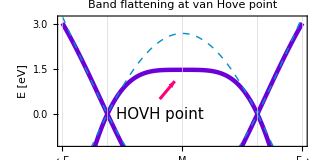

```mathematica
plt=Graphics[{
Inset[FSplot,{0,-1}.57],
Inset[BandsRenorm,{0.0,1.}],
Inset[lgnd,{0+.665,1.26}(*{0.1,0.83}*)],
SText["(a)",{-0.9,1.5}],
SText["(b)",{-0.9,0.35}]
},PlotRange->{{-1,1},{-1,1}1.55},ImageSize->320]
Export[FileNameJoin[{NotebookDirectory[],"Fig_Reno_FS_new.pdf"}],plt];
```